```mathematica
(* 1.1.3.4 *)
-Graphics-
(* Условие *)
-Graphics-
-Graphics-
(* Решение *)
(* 1. Динамика системы по стандартной функции Гамильтона *)
(* Запишем функцию Гамильтона для шарика, подвешенного на нити и совершающего малые колебания координтах: импульс - координата *)
```

```mathematica
ℋ = p[t]^2/(2 m)+ (m g x[t]^2)/(2 l)
```

p[t]^2/(2 m)+(g m x[t]^2)/(2 l)

```mathematica
(* Теперь запишем уравнения Гамильтона для такой системы и найдем их решения *)
```

```mathematica
D[p[t], t] = - D[ℋ, x[t]]
```

-(g m x[t])/l

```mathematica
D[x[t], t] =  D[ℋ, p[t]]
```

p[t]/m

```mathematica
FullSimplify[DSolve[{D[p[t], t] == - D[ℋ, x[t]],D[x[t], t] ==  D[ℋ, p[t]], x[0]==0,p[0]==1},{x[t],p[t]},t]]
```

{{p[t]→Cos[(√g t)/(√l)],x[t]→(√l Sin[(√g t)/(√l)])/(√g m)}}

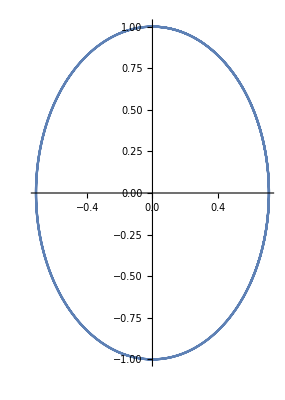

```mathematica
(* Построим фазовый портрет нашей системы при разных длинах нити *)
ParametricPlot[{(√l Sin[(√g t)/(√l)])/(√g m),Cos[(√g t)/(√l)]}/.{g ->9.8, l->5,m->1},{t,0,15}]
```

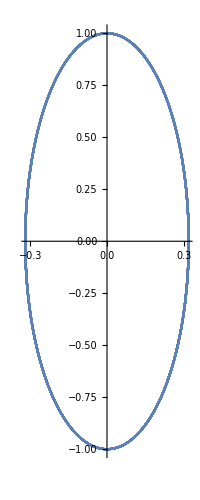

```mathematica
ParametricPlot[{(√l Sin[(√g t)/(√l)])/(√g m),Cos[(√g t)/(√l)]}/.{g ->9.8, l->1,m->1},{t,0,15}]
```

```mathematica
(* Также построим "топографический портрет" функции Гамильтона при этих же параметрах*)
```

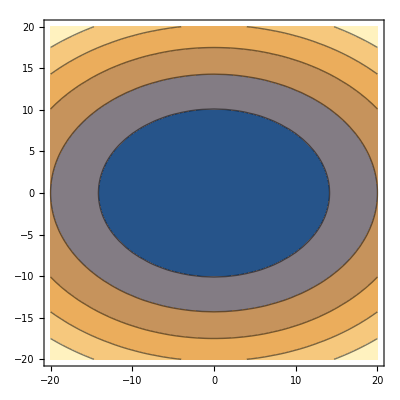

```mathematica
ContourPlot[p^2/(2 m)+ (m g x^2)/(2 l)/.{g ->9.8, l->5,m->1},{p,-20,20},{x,-20,20}]
```

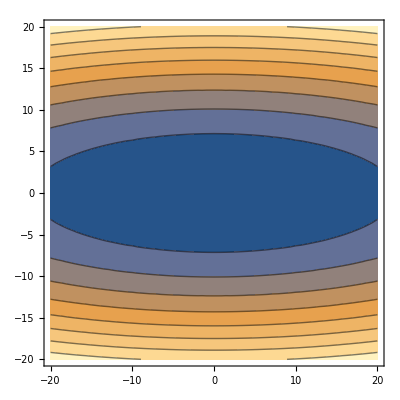

```mathematica
ContourPlot[p^2/(2 m)+ (m g x^2)/(2 l)/.{g ->9.8, l->1,m->1},{p,-20,20},{x,-20,20}]
```

```mathematica
(* Можно заметить, что эти портреты сжимаются и разжимаются при разных длинах нити, отсюда делаем вывод, что энергия этой системы прямым образом зависит от длины нити. Также из фазовых траекторий видно, что также будут меняться и амплитуды колебаний. *)
```

```mathematica
(* 2. Зависимость энергии. *)
(* Осуществим некоторые преобразования для того, чтобы найти явную зависимость энергии маятника от длины нити. Для этого вспомним, что такое циклическая частота и попробуем использовать это знания для преобразования нашей функции Гамильтона. *)
```

```mathematica
Subscript[ω, 0]=√(g/l)(* циклическая частота колебаний математического маятника. *)
```

```mathematica
(* Попробуем выделить циклическую частоту в написанной выше функции Гамильтона. *)
```

```mathematica
ℋ1 = 1/2 √(g/l)(1/m √(l/g)p[t]^2+ m √(g/l)x[t]^2)
```

1/2 √(g/l) ((√(l/g) p[t]^2)/m+√(g/l) m x[t]^2)

```mathematica
(* А теперь произведем замену фазовых координат *)
```

```mathematica
1/m √(l/g)p[t]^2 = P[t] ^2     ->     p[t] = (g/l)^(1/4)√m P[t]
m √(g/l)x[t]^2 = X[t]^2      ->     x[t] = 1/(√m)(l/g)^(1/4) X[t]
```

```mathematica
ℋ1/.{p[t] ->(g/l)^(1/4)√m P[t],x[t]->1/(√m)(l/g)^(1/4) X[t]}
```

```mathematica
ℋnew=1/2 √(g/l)(P[t]^2+X[t]^2)
```

1/2 √(g/l) (P[t]^2+X[t]^2)

```mathematica
(* Теперь фазовые координаты имеют одну размерность - размерность корня из действия, т.е. с медленным изменением какой-либо из величин, величина действия сохраняется , но у нас есть частота,которая будет менять энергии матяника (топографический портрет будет выглядеть как вложенные окружности разных радиусов (энергий)), а значит величина энергии напрямую определяется ТОЛЬКО длиной нити, таким образом: *)
```

```mathematica
E ∼1/(√l)
```

```mathematica
(* Чем короче нить, тем больше энергия колебаний *)
```

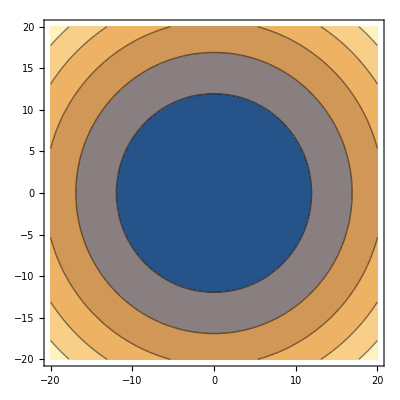

```mathematica
ContourPlot[1/2 √(g/l)(P^2+X^2)/.{g ->9.8, l->5,m->1},{P,-20,20},{X,-20,20}]
```

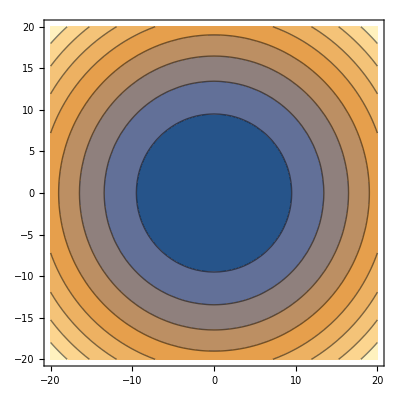

```mathematica
ContourPlot[1/2 √(g/l)(P^2+X^2)/.{g ->9.8, l->0.5,m->1},{P,-20,20},{X,-20,20}]
```

```mathematica
(* 3. "дейвствие - угол" *)
(* Поскольку площадь нашей концентрической окружности - это действие, в терминах X/P, то есть: *)
S = 2π ×1/2(P[t]^2+X[t]^2) = π(P[t]^2+X[t]^2)(* Мы не вносим частоту, поскольку она не определяет действие *)
```

```mathematica
(* Значит переменная действия это (по своему опрделению) : действие, деленное на 2π. Это означает, что фаза обхода нашей траектори будет определяется углом в 2π, то есть мы смотрим величину площади в единицу нашей фазы *)
```

```mathematica
ℐ = 1/(2π)π(P[t]^2+X[t]^2)=1/2(P[t]^2+X[t]^2)
```

```mathematica
(* Мы нашли первую новую координату  - координату действия. Теперь мы можем переписать уравнения Гамильтона в систему "действия - угол" , поскольку координата "угол" канонически сопряжена с координатой  "действие" то записываться это будет так *)
```

```mathematica
ℐ =1/2(P[t]^2+X[t]^2)
```

```mathematica
ℋaction =√(g/l)ℐ[t]
```

√(g/l) (1/2 (P[t]^2+X[t]^2))[t]

```mathematica
(* Решим уравнения Гамильтона в терминах X/P *)
DSolve[{D[P[t], t] ==-D[ℋnew, X[t]],D[X[t], t]==D[ℋnew, P[t]],X[0]==0,P[0]==1},{X[t],P[t]},t]
```

{{P[t]→Cos[√(g/l) t],X[t]→Sin[√(g/l) t]}}

```mathematica
(* Теперь переведем их в термины наших старых x/p *)
```

```mathematica
p[t] -> (g/l)^(1/4)√m Cos[√(g/l) t]
x[t] -> 1/(√m)(l/g)^(1/4) Sin[√(g/l) t]
```

p[t]→(g/l)^(1/4) √m Cos[√(g/l) t]

x[t]→((l/g)^(1/4) Sin[√(g/l) t])/(√m)

```mathematica
(* Наконец-то,  перейдем в "действие - угол" *)
ℐ1 = 1/2(Cos[√(g/l) t]^2+Sin[√(g/l) t]^2)
```

1/2 (Cos[√(g/l) t]^2+Sin[√(g/l) t]^2)

```mathematica
D[ℐ, t] ==0
D[Θ, t]==D[ℋaction, ℐ]
```

```mathematica
DSolve[{D[ℐ[t], t] ==0,D[Θ[t], t]==D[ℋaction, ℐ[t]],ℐ[0]==1,Θ[0]==1},{ℐ[t],Θ[t]},t]
```

{{ℐ[t]→1,Θ[t]→1+√(g/l) t}}

```mathematica
(* То есть координата "действие" явялется постоянной величиной в любой момент времени, а координата "угол" - просто линейная функция от циклической частоты *)
```

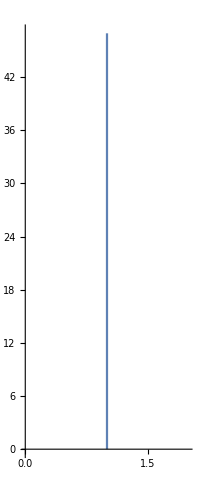

```mathematica
ParametricPlot[{1,√(g/l) t}/.{g ->9.8, l->1},{t,0,15}]
```

```mathematica
(*Зная величину переменной действия, можно найти и саму величину действия - это будет площадь соответсвующей окржуности, как переменная действия, умноженная на 2π *)
```

```mathematica
S = 2π 1
```

2 π

```mathematica
(*А с учетом того факта, что  S = π(P[t]^2+X[t]^2), то (P[t]^2+X[t]^2) = 2 - уравнение окружности радиуса 2 (окружности, определяющей энергетический уровень, заданный с помощью заданных нами начальных условий). Можно сказать, что величины "действие - угол" помогают однозначно описать динамику системы *)
```